### Start choosing the example:

```mathematica
t="Jamaratv9";
beta =0;
A = 0.2;
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"];
g[x]
```

Log[x]

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4,5,6,7,8,9},Adjacency Matrix→{{0,1,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0},{0,0,0,1,1,0,0,0,0},{0,0,0,0,0,1,0,0,0},{0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0}},Entrance Vertices and Currents→{{1,I1},{2,I2}},Exit Vertices and Terminal Costs→{{7,U1},{8,U2},{9,U3}},Switching Costs→{}|>

### Look at the output bellow before trying to rerun!

```mathematica
(*With U2->2, agents don't exit through 6. running with U2->U2 to determine the largest value for which we get some current, hence unicity.*)
```

```mathematica
{timeHdata,d2eH}=AbsoluteTiming@D2E[Data/.{I1-> 20,I2->20, U1-> 10,U2->10,U3->0}];
timeHdata
{timeH,{systemH,rulesH}}=AbsoluteTiming@CriticalCongestionSolver[d2eH];
timeH
```

0.104387

Time to solve critical congestion equations only: 
0.001837

2.49211

```mathematica
ColorNetworkByValueFunctionOperator[d2eH][rulesH]
```

0.261258

```mathematica
d2eH["uvars"]/.rulesH
```

<|{1,1->2}→70,{1,1->3}→70,{2,2->4}→70,{3,3->4}→50,{3,3->5}→50,{4,4->6}→50,{5,5->6}→30,{5,5->7}→30,{6,6->8}→30,{7,7->9}→10,{7,7->ex7}→10,{8,8->9}→10,{8,8->ex8}→10,{9,9->ex9}→0,{en1,en1->1}→70,{en2,en2->2}→70,{2,1->2}→70,{3,1->3}→50,{4,2->4}→50,{4,3->4}→50,{5,3->5}→30,{6,4->6}→30,{6,5->6}→30,{7,5->7}→10,{8,6->8}→10,{9,7->9}→0,{ex7,7->ex7}→10,{9,8->9}→0,{ex8,8->ex8}→10,{ex9,9->ex9}→0,{1,en1->1}→70,{2,en2->2}→70|>

```mathematica
{timeheterodata,d2ehetero}=AbsoluteTiming[D2E[Data/.{I1-> 1,I2->2, U1-> 1,U2->2,U3->3}]];
timeheterodata
{timehetero,{systemhetero,resulthetero}}=AbsoluteTiming@CriticalCongestionSolver[d2ehetero];
timehetero
```

0.101263

Time to solve critical congestion equations only: 
0.001867

4.12175

0.149031

4.8388

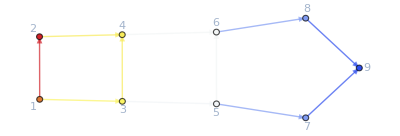

```mathematica
ColorNetworkByValueFunction[d2ehetero]
```

```mathematica
d2e=D2E[Data/.{I1-> 2,I2->6, U1-> 1,U2->2,U3->0}];
{time,{system,rules}}=CriticalCongestionSolver[d2e]//AbsoluteTiming
```

{4.05379,{True,<|u17→584/41,u2→523/41,u26→0,u28→0,u3→584/41,u4→380/41,u5→380/41,u6→399/41,u7→218/41,u8→218/41,u9→233/41,j11→136/41,j13→69/41,j14→3,j15→2,j16→6,j17→61/41,j2→143/41,j24→0,j25→0,j27→0,j29→0,j3→185/41,j30→0,j31→0,j32→0,j4→0,j5→162/41,j6→166/41,j7→0,j8→177/41,j9→151/41,jt1→61/41,jt10→0,jt11→61/41,jt12→185/41,jt14→143/41,jt15→0,jt16→19/41,jt17→0,jt18→0,jt2→0,jt20→166/41,jt21→0,jt22→0,jt23→0,jt24→0,jt26→162/41,jt27→0,jt28→15/41,jt29→0,jt3→0,jt30→0,jt31→15/41,jt32→151/41,jt33→0,jt34→0,jt36→0,jt37→1,jt38→136/41,jt4→0,jt40→0,jt41→0,jt42→0,jt43→2,jt44→69/41,jt46→0,jt47→0,jt48→0,jt49→0,jt5→0,jt50→1,jt51→0,jt52→2,jt53→0,jt54→0,jt6→2,jt7→0,jt8→0,jt9→0,u1→523/41,u11→1,u12→2,u13→2,u14→0,u18→380/41,u19→399/41,u20→399/41,u21→218/41,u22→233/41,u23→233/41,u24→1,u25→2,u27→1,u29→2,u30→0,u31→523/41,u32→584/41,j1→0,j10→1,j12→2,j18→0,j19→0,j20→19/41,j21→0,j22→0,j23→15/41,j26→0,j28→0,jt13→0,jt19→19/41,jt25→0,jt35→0,jt39→0,jt45→0,u10→1,u15→523/41,u16→584/41|>}}

```mathematica
{time1data,d2e1}=AbsoluteTiming@D2E[Data/.{I1-> 2.00000000001515151515151515115151515115151515151551515151,I2->6, U1-> 3,U2->3,U3->0.}];
time1data
```

0.276266

```mathematica
rules=First@Solve[d2e1["EqCriticalCase"]]//Quiet;
```

```mathematica
system = d2e1["EqAllAll"]/.rules;
```

```mathematica
{system,rules}=CriticalCongestionStep[{system,rules}]
```

True

{True,<|u17→645/41,u2→585/41,u26→0,u28→0,u3→645/41,u4→443/41,u5→443/41,u6→459/41,u7→285/41,u8→285/41,u9→289/41,j11→39/41,j13→43/41,j14→6,j15→2,j16→6,j17→60/41,j2→142/41,j24→0,j25→0,j27→0,j29→0,j3→186/41,j30→0,j31→0,j32→0,j4→0,j5→158/41,j6→170/41,j7→0,j8→162/41,j9→166/41,jt1→60/41,jt10→0,jt11→60/41,jt12→186/41,jt14→142/41,jt15→0,jt16→16/41,jt17→0,jt18→0,jt2→0,jt20→170/41,jt21→0,jt22→0,jt23→0,jt24→0,jt26→158/41,jt27→0,jt28→4/41,jt29→0,jt3→0,jt30→0,jt31→4/41,jt32→166/41,jt33→0,jt34→0,jt36→0,jt37→3,jt38→39/41,jt4→0,jt40→0,jt41→0,jt42→0,jt43→3,jt44→43/41,jt46→0,jt47→0,jt48→0,jt49→0,jt5→0,jt50→3,jt51→0,jt52→3,jt53→0,jt54→0,jt6→2,jt7→0,jt8→0,jt9→0,u1→585/41,u11→3,u12→3,u13→3,u14→0.,u18→443/41,u19→459/41,u20→459/41,u21→285/41,u22→289/41,u23→289/41,u24→3,u25→3,u27→3,u29→3,u30→0.,u31→585/41,u32→645/41,j1→0,j10→3,j12→3,j18→0,j19→0,j20→16/41,j21→0,j22→0,j23→4/41,j26→0,j28→0,jt13→0,jt19→16/41,jt25→0,jt35→0,jt39→0,jt45→0,u10→3,u15→585/41,u16→645/41|>}

```mathematica
{time1,{system1,rules1}}=CriticalCongestionSolver[d2e1]//AbsoluteTiming
```

j1==0&&j10==3&&j12==3&&j18==0&&j19==0&&41 j20==16&&j21==0&&j22==0&&41 j23==4&&j26==0&&j28==0&&jt13==0&&41 jt19==16&&jt25==0&&jt35==0&&jt39==0&&jt45==0&&u10==3&&41 u15==585&&41 u16==645

True

True

{1.33651,{True,<|u17→645/41,u2→585/41,u26→0,u28→0,u3→645/41,u4→443/41,u5→443/41,u6→459/41,u7→285/41,u8→285/41,u9→289/41,j11→39/41,j13→43/41,j14→6,j15→2,j16→6,j17→60/41,j2→142/41,j24→0,j25→0,j27→0,j29→0,j3→186/41,j30→0,j31→0,j32→0,j4→0,j5→158/41,j6→170/41,j7→0,j8→162/41,j9→166/41,jt1→60/41,jt10→0,jt11→60/41,jt12→186/41,jt14→142/41,jt15→0,jt16→16/41,jt17→0,jt18→0,jt2→0,jt20→170/41,jt21→0,jt22→0,jt23→0,jt24→0,jt26→158/41,jt27→0,jt28→4/41,jt29→0,jt3→0,jt30→0,jt31→4/41,jt32→166/41,jt33→0,jt34→0,jt36→0,jt37→3,jt38→39/41,jt4→0,jt40→0,jt41→0,jt42→0,jt43→3,jt44→43/41,jt46→0,jt47→0,jt48→0,jt49→0,jt5→0,jt50→3,jt51→0,jt52→3,jt53→0,jt54→0,jt6→2,jt7→0,jt8→0,jt9→0,u1→585/41,u11→3,u12→3,u13→3,u14→0.,u18→443/41,u19→459/41,u20→459/41,u21→285/41,u22→289/41,u23→289/41,u24→3,u25→3,u27→3,u29→3,u30→0.,u31→585/41,u32→645/41,j1→0,j10→3,j12→3,j18→0,j19→0,j20→16/41,j21→0,j22→0,j23→4/41,j26→0,j28→0,jt13→0,jt19→16/41,jt25→0,jt35→0,jt39→0,jt45→0,u10→3,u15→585/41,u16→645/41|>}}

#### Non-linear case

```mathematica
(*Don't forget to change the Range!*)
alpha =1;
MFGEquations = d2e1;
FFR=rules1;
pop=(#-> Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, PlotLabel->#,(*PlotRange->{-0.1,2.4},*)GridLines->Automatic,ImageSize->90])&/@MFGEquations["BEL"];
```

```mathematica
val=(#-> Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, PlotLabel->#,(*PlotRange->{-0.1,4.7},*)GridLines->Automatic,ImageSize->90])&/@MFGEquations["BEL"];
```

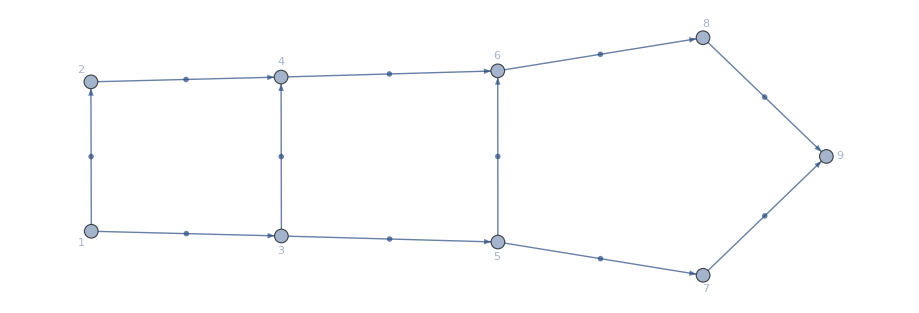

-Graphics-

```mathematica
Graph[d2e1["BG"],EdgeLabels-> pop,GraphLayout->"SpringElectricalEmbedding"]
Graph[d2e1["BG"],EdgeLabels-> val,GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
alpha = .1;
{timeFFR,FFR}= AbsoluteTiming[Catch@FixedPoint[FixedReduceX1[d2e1],rules1,200]//N//KeySort]
```

The error (1-Norm of LHS-RHS) is 2.16836

The error (1-Norm of LHS-RHS) is 0.483755

The error (1-Norm of LHS-RHS) is 0.390939

The error (1-Norm of LHS-RHS) is 0.316361

The error (1-Norm of LHS-RHS) is 0.256598

The error (1-Norm of LHS-RHS) is 0.208939

The error (1-Norm of LHS-RHS) is 0.171176

The error (1-Norm of LHS-RHS) is 0.140463

The error (1-Norm of LHS-RHS) is 0.115598

The error (1-Norm of LHS-RHS) is 0.0952329

The error (1-Norm of LHS-RHS) is 0.0785155

The error (1-Norm of LHS-RHS) is 0.0647735

The error (1-Norm of LHS-RHS) is 0.0534638

The error (1-Norm of LHS-RHS) is 0.0441468

The error (1-Norm of LHS-RHS) is 0.0364652

The error (1-Norm of LHS-RHS) is 0.0301278

The error (1-Norm of LHS-RHS) is 0.0248968

The error (1-Norm of LHS-RHS) is 0.0205772

The error (1-Norm of LHS-RHS) is 0.0170091

The error (1-Norm of LHS-RHS) is 0.0140609

The error (1-Norm of LHS-RHS) is 0.0116246

The error (1-Norm of LHS-RHS) is 0.00961097

The error (1-Norm of LHS-RHS) is 0.00794645

The error (1-Norm of LHS-RHS) is 0.00657041

The error (1-Norm of LHS-RHS) is 0.00543277

The error (1-Norm of LHS-RHS) is 0.0044922

The error (1-Norm of LHS-RHS) is 0.00371451

The error (1-Norm of LHS-RHS) is 0.00307149

The error (1-Norm of LHS-RHS) is 0.0025398

The error (1-Norm of LHS-RHS) is 0.00210016

The error (1-Norm of LHS-RHS) is 0.00173662

The error (1-Norm of LHS-RHS) is 0.00143602

The error (1-Norm of LHS-RHS) is 0.00118746

The error (1-Norm of LHS-RHS) is 0.000981918

The error (1-Norm of LHS-RHS) is 0.000811957

The error (1-Norm of LHS-RHS) is 0.000671415

The error (1-Norm of LHS-RHS) is 0.0005552

The error (1-Norm of LHS-RHS) is 0.0004591

The error (1-Norm of LHS-RHS) is 0.000379635

The error (1-Norm of LHS-RHS) is 0.000313924

The error (1-Norm of LHS-RHS) is 0.000259587

The error (1-Norm of LHS-RHS) is 0.000214655

The error (1-Norm of LHS-RHS) is 0.000177501

The error (1-Norm of LHS-RHS) is 0.000146777

The error (1-Norm of LHS-RHS) is 0.000121372

The error (1-Norm of LHS-RHS) is 0.000100363

The error (1-Norm of LHS-RHS) is 0.0000829916

The error (1-Norm of LHS-RHS) is 0.0000686266

The error (1-Norm of LHS-RHS) is 0.0000567481

The error (1-Norm of LHS-RHS) is 0.0000469256

The error (1-Norm of LHS-RHS) is 0.0000388032

The error (1-Norm of LHS-RHS) is 0.0000320868

The error (1-Norm of LHS-RHS) is 0.000026533

The error (1-Norm of LHS-RHS) is 0.0000219403

The error (1-Norm of LHS-RHS) is 0.0000181427

The error (1-Norm of LHS-RHS) is 0.0000150024

The error (1-Norm of LHS-RHS) is 0.0000124056

The error (1-Norm of LHS-RHS) is 0.0000102583

The error (1-Norm of LHS-RHS) is 8.48266×10^-6

The error (1-Norm of LHS-RHS) is 7.01442×10^-6

The error (1-Norm of LHS-RHS) is 5.8004×10^-6

The error (1-Norm of LHS-RHS) is 4.79638×10^-6

The error (1-Norm of LHS-RHS) is 3.96614×10^-6

The error (1-Norm of LHS-RHS) is 3.2796×10^-6

$Aborted

```mathematica
rules0=AssociationThread[d2e1["js"],Table[0,{i,1,Length@d2e1["js"]}]];
alpha = .1;
{timeFFR,FFR}= AbsoluteTiming@KeySort@N@Catch@FixedPoint[FixedReduceX1[d2e1],rules0, 2]
```

The error (1-Norm of LHS-RHS) is 16.0128

The error (1-Norm of LHS-RHS) is 0.586457

{12.0271,<|j1→0.,j10→0.,j11→3.97189,j12→0.,j13→4.17963,j14→0.,j15→2.15152,j16→6.,j17→1.27503,j18→0.,j19→0.,j2→3.42655,j20→0.41023,j21→0.,j22→0.,j23→0.135112,j24→0.,j25→0.,j26→0.,j27→0.,j28→0.,j29→0.,j3→4.72497,j30→0.,j31→0.,j32→0.,j4→0.,j5→3.83678,j6→4.31474,j7→0.,j8→3.97189,j9→4.17963,jt1→1.27503,jt10→0.,jt11→1.27503,jt12→4.72497,jt13→0.,jt14→3.42655,jt15→0.,jt16→0.41023,jt17→0.,jt18→0.,jt19→0.41023,jt2→0.,jt20→4.31474,jt21→0.,jt22→0.,jt23→0.,jt24→0.,jt25→0.,jt26→3.83678,jt27→0.,jt28→0.135112,jt29→0.,jt3→0.,jt30→0.,jt31→0.135112,jt32→4.17963,jt33→0.,jt34→0.,jt35→0.,jt36→0.,jt37→0.,jt38→3.97189,jt39→0.,jt4→0.,jt40→0.,jt41→0.,jt42→0.,jt43→0.,jt44→4.17963,jt45→0.,jt46→0.,jt47→0.,jt48→0.,jt49→0.,jt5→0.,jt50→0.,jt51→0.,jt52→0.,jt53→0.,jt54→0.,jt6→2.15152,jt7→0.,jt8→0.,jt9→0.,u1→4.11369,u10→0.,u11→0.,u12→0.,u13→0.,u14→0.,u15→4.11369,u16→4.88636,u17→4.88636,u18→2.82175,u19→3.1842,u2→4.11369,u20→3.1842,u21→1.43818,u22→1.5651,u23→1.5651,u24→0.,u25→0.,u26→0.,u27→0.,u28→0.,u29→0.,u3→4.88636,u30→0.,u31→4.11369,u32→4.88636,u4→2.82175,u5→2.82175,u6→3.1842,u7→1.43818,u8→1.43818,u9→1.5651|>}

### The nonlinear solver solves the critical congestion case when the alpha is 1 and the initial currents are all zero.

```mathematica
rules0=AssociationThread[d2e1["js"],Table[0,{i,1,Length@d2e1["js"]}]];
alpha = 1;
{timeFFR,FFR}= AbsoluteTiming@Catch@FixedPoint[FixedReduceX1[d2e1],rules0, 1]
d2e1["EqCriticalCase"]/.FFR
```

The error (1-Norm of LHS-RHS) is 3.63043×10^-14

The error is 3.63043×10^-14 which is less than 1.×10^-10

{1.3094,<|u17→645/41,u2→585/41,u26→0,u28→0,u3→645/41,u4→443/41,u5→443/41,u6→459/41,u7→285/41,u8→285/41,u9→289/41,j11→39/41,j13→43/41,j14→6,j15→2,j16→6,j17→60/41,j2→142/41,j24→0,j25→0,j27→0,j29→0,j3→186/41,j30→0,j31→0,j32→0,j4→0,j5→158/41,j6→170/41,j7→0,j8→162/41,j9→166/41,jt1→60/41,jt10→0,jt11→60/41,jt12→186/41,jt14→142/41,jt15→0,jt16→16/41,jt17→0,jt18→0,jt2→0,jt20→170/41,jt21→0,jt22→0,jt23→0,jt24→0,jt26→158/41,jt27→0,jt28→4/41,jt29→0,jt3→0,jt30→0,jt31→4/41,jt32→166/41,jt33→0,jt34→0,jt36→0,jt37→3,jt38→39/41,jt4→0,jt40→0,jt41→0,jt42→0,jt43→3,jt44→43/41,jt46→0,jt47→0,jt48→0,jt49→0,jt5→0,jt50→3,jt51→0,jt52→3,jt53→0,jt54→0,jt6→2,jt7→0,jt8→0,jt9→0,u1→585/41,u11→3,u12→3,u13→3,u14→0.,u18→443/41,u19→459/41,u20→459/41,u21→285/41,u22→289/41,u23→289/41,u24→3,u25→3,u27→3,u29→3,u30→0.,u31→585/41,u32→645/41,j1→0,j10→3,j12→3,j18→0,j19→0,j20→16/41,j21→0,j22→0,j23→4/41,j26→0,j28→0,jt13→0,jt19→16/41,jt25→0,jt35→0,jt39→0,jt45→0,u10→3,u15→585/41,u16→645/41|>}

True

```mathematica
d2e=d2ehetero;
rules0=AssociationThread[d2e1["js"],Table[0,{i,1,Length@d2e["js"]}]];
alpha = 1;
{timeFFR,FFR}= AbsoluteTiming@KeySort@Catch@FixedPoint[FixedReduceX1[d2e],rules0, 1]
d2e["EqCriticalCase"]/.FFR
```

The error (1-Norm of LHS-RHS) is 1.20737×10^-14

The error is 1.20737×10^-14 which is less than 3.×10^-1

{2.60519,<|j1→0,j10→0,j11→193/82,j12→1/2,j13→53/82,j14→0,j15→1,j16→2,j17→16/41,j18→0,j19→0,j2→57/41,j20→7/41,j21→0,j22→0,j23→12/41,j24→0,j25→0,j26→1/2,j27→0,j28→0,j29→0,j3→66/41,j30→0,j31→0,j32→0,j4→0,j5→64/41,j6→59/41,j7→0,j8→76/41,j9→47/41,jt1→16/41,jt10→0,jt11→16/41,jt12→66/41,jt13→0,jt14→57/41,jt15→0,jt16→7/41,jt17→0,jt18→0,jt19→7/41,jt2→0,jt20→59/41,jt21→0,jt22→0,jt23→0,jt24→0,jt25→0,jt26→64/41,jt27→0,jt28→12/41,jt29→0,jt3→0,jt30→0,jt31→12/41,jt32→47/41,jt33→0,jt34→0,jt35→0,jt36→0,jt37→0,jt38→76/41,jt39→0,jt4→0,jt40→1/2,jt41→0,jt42→0,jt43→1/2,jt44→53/82,jt45→0,jt46→0,jt47→0,jt48→0,jt49→0,jt5→0,jt50→0,jt51→1/2,jt52→0,jt53→0,jt54→0,jt6→1,jt7→0,jt8→0,jt9→0,u1→238/41,u10→1,u11→1,u12→2,u13→2,u14→3,u15→238/41,u16→254/41,u17→254/41,u18→181/41,u19→188/41,u2→238/41,u20→188/41,u21→117/41,u22→129/41,u23→129/41,u24→1,u25→2,u26→3/2,u27→1,u28→3/2,u29→2,u3→254/41,u30→3,u31→238/41,u32→254/41,u4→181/41,u5→181/41,u6→188/41,u7→117/41,u8→117/41,u9→129/41|>}

True

### Color representation of the value function (this is suitable for the critical congestion case because the value function is linear on each edge)

#### New function!!!

```mathematica
eStyle[colors_][pts_,DirectedEdge[x_,y_]]:={colors[[y]],Arrow[Line[pts,VertexColors->{colors[[x]],colors[[y]]}]]}

ColorNetworkByValueFunctionOperator[d2e1_Association][rules_]:= Module[{values,colors},
values=d2e1["VL"]/.KeyMap[#[[1]]&,d2e1["uvars"]/.rules];
(*Print[values];*)
colors=ColorData["TemperatureMap"]/@(values/Max[values]);
(*Print[colors];*)
GraphicsGrid[{
{HighlightGraph[SetProperty[d2e1["BG"],EdgeShapeFunction-> eStyle[colors]],Thread[Style[d2e1["VL"],colors]],GraphLayout->"SpringEmbedding"]},
{BarLegend["TemperatureMap",LegendMarkerSize->100,LegendLayout->"ReversedRow"]}
}]
]
```

### Idea:

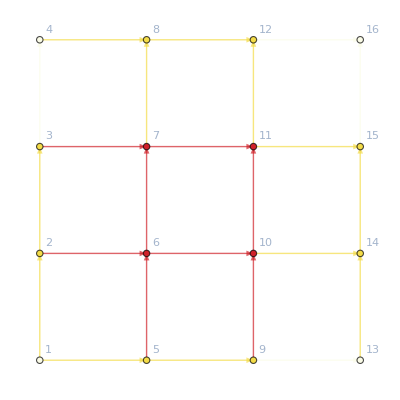

```mathematica
eStyle[colors_][pts_,DirectedEdge[x_,y_]]:={colors[[y]],Arrow[Line[pts,VertexColors->{colors[[x]],colors[[y]]}]]}
g=GridGraph[{4,4},VertexLabels->"Name",ImagePadding->10,DirectedEdges->True];
colors=ColorData["TemperatureMap"]/@(VertexDegree[g]/Max[VertexDegree[g]]);
HighlightGraph[SetProperty[g,EdgeShapeFunction->eStyle[colors]],Thread[Style[VertexList[g],colors]]]
```

### Test on a “large” network

#### D2E already takes half a minute. Set the option of giving the Graph with GridGraph, for example. Would this run faster?

```mathematica
eme=3;
ene=3;
gr=GridGraph[{eme,ene},DirectedEdges->True];
Data =AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{1,I1}/.I1->400},(*FinalCosts=*){{eme*ene,U1}/.U1->0},(*SwitchingCostsData=*){}}];
{timegridata,d2egrid}=AbsoluteTiming@D2E[Data];
d2egrid["FG"];
timegridata;
timegridata
```

0.158782

```mathematica
alpha=.1;
rulesgrid = Solver[d2egrid][alpha]
```

$Aborted

```mathematica
d2egrid["Nrhs"]/.rulesgrid
```

{-1.98952×10^-13,-2.27374×10^-13,-8.52651×10^-14,-1.13687×10^-13,-8.52651×10^-14,-8.52651×10^-14,-1.42109×10^-13,-6.39488×10^-14,-1.42109×10^-13,-1.42109×10^-13,-6.39488×10^-14,-8.52651×10^-14,-8.52651×10^-14,-1.13687×10^-13,-2.27374×10^-13,-8.52651×10^-14,-1.98952×10^-13}

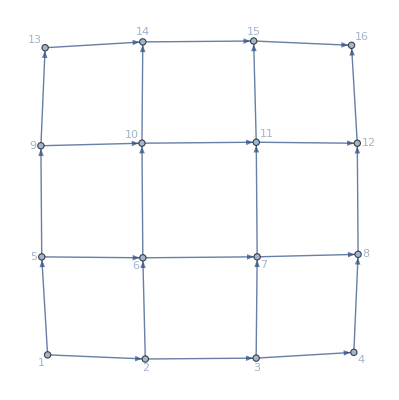
ColorNetworkByValueFunctionOperator[<|Data→<|Vertices List→{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},Adjacency Matrix→SparseArray[…],Entrance Vertices and Currents→{{1,400}},Exit Vertices and Terminal Costs→{{16,0}},Switching Costs→{}|>,BG→-Graphics-,EntranceVertices→{1},46,EqCriticalCase→1,Nrhs→{j1-j27+IntM[j1-j27,1->2],j2-j28+IntM[j2-j28,1->5],21,j24-j50+IntM[j24-j50,15->16]},EqGeneralCase→1|>][1]
 |  |  |  |

```mathematica
ColorNetworkByValueFunctionOperator[d2egrid][rulesgrid]
```

```mathematica
{timegrid,{systemgrid,rulesgrid}}=AbsoluteTiming@CriticalCongestionSolver[d2egrid];
timegrid
```

2.1905

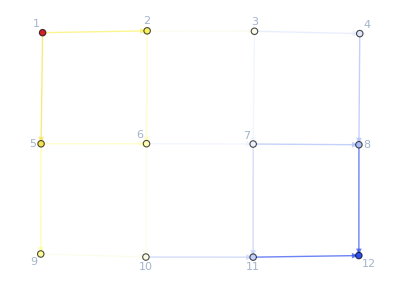

```mathematica
rulesgrid=KeySort@rulesgrid;
ColorNetworkByValueFunctionOperator[d2egrid][rulesgrid]
```

```mathematica
f[x_Integer]:= b
```

```mathematica
f[4]
```

b

```mathematica
rules0=AssociationThread[d2egrid["js"],Table[0,{i,1,Length@d2egrid["js"]}]];
alpha = 1;
{timeFFR,FFR}= AbsoluteTiming@Catch@FixedPoint[FixedReduceX1[d2egrid],rules0, 1]
d2egrid["EqCriticalCase"]/.FFR
```

The error (1-Norm of LHS-RHS) is 2.14584×10^-12

The error is 2.14584×10^-12 which is less than 1.×10^-10

{1.76439,<|u20→11200/23,u21→35600/69,u29→20000/69,u3→11200/23,u30→24400/69,u31→12800/69,u32→14800/69,u33→0,u34→24400/69,u35→14800/69,u36→0,u4→11200/23,u5→8000/23,u6→8000/23,u7→800/3,u8→35600/69,u9→35600/69,j15→5600/69,j16→3200/23,j17→14800/69,j18→400,j19→400,j20→0,j21→0,j22→0,j24→0,j26→0,j28→0,j29→0,j3→3200/23,j30→0,j31→0,j32→0,j33→0,j37→0,j38→0,j4→5200/69,j5→5600/69,j6→4000/69,j7→5600/69,j8→2400/23,j9→5600/69,jt1→0,jt11→0,jt12→0,jt15→0,jt16→0,jt17→0,jt18→0,jt19→5600/69,jt2→0,jt20→0,jt22→5600/69,jt23→0,jt24→0,jt25→0,jt26→0,jt29→5200/69-jt28,jt3→0,jt30→2800/23-jt28-jt31,jt32→-400/23+jt28,jt35→0,jt36→-2800/23+jt28+jt31,jt37→0,jt38→2800/23-jt28-jt31,jt4→0,jt40→4000/69-jt41,jt42→5200/69-jt41-jt44,jt43→3200/69+jt41,jt45→-5200/69+jt41+jt44,jt46→0,jt47→5200/69-jt41-jt44,jt5→14800/69,jt50→0,jt51→0,jt53→0,jt54→2400/23,jt56→0,jt57→5600/69,jt58→0,jt59→0,jt6→12800/69,jt60→4000/69,jt61→0,jt62→5600/69,jt64→0,jt65→0,jt66→5200/69,jt67→0,jt68→3200/23,jt7→3200/23,jt70→0,jt71→0,jt72→12800/69,jt73→0,jt74→14800/69,jt75→0,jt76→0,jt8→5200/69,jt9→0,u1→48400/69,u10→28400/69,u11→28400/69,u12→20000/69,u13→20000/69,u15→10000/23,u16→24400/69,u17→14800/69,u18→0,u2→48400/69,u22→8000/23,u23→28400/69,u24→800/3,u25→20000/69,u26→12800/69,u27→28400/69,u28→10000/23,u37→0,u38→48400/69,j1→14800/69,j10→2800/23,j11→4000/69,j12→2400/23,j13→5200/69,j14→12800/69,j2→12800/69,j23→0,j25→0,j27→0,j34→0,j35→0,j36→0,jt10→0,jt13→5600/69,jt14→4000/69,jt21→2400/23,jt27→0,jt33→0,jt34→0,jt39→0,jt48→0,jt49→0,jt52→5600/69,jt55→0,jt63→0,jt69→0,u14→12800/69,u19→48400/69|>}

True

```mathematica
Solver[d2egrid][1]
```

The error (1-Norm of LHS-RHS) is 2.14584×10^-12

The error is 2.14584×10^-12 which is less than 1.×10^-10

It took 1.509 to solve!

<|u20→11200/23,u21→35600/69,u29→20000/69,u3→11200/23,u30→24400/69,u31→12800/69,u32→14800/69,u33→0,u34→24400/69,u35→14800/69,u36→0,u4→11200/23,u5→8000/23,u6→8000/23,u7→800/3,u8→35600/69,u9→35600/69,j15→5600/69,j16→3200/23,j17→14800/69,j18→400,j19→400,j20→0,j21→0,j22→0,j24→0,j26→0,j28→0,j29→0,j3→3200/23,j30→0,j31→0,j32→0,j33→0,j37→0,j38→0,j4→5200/69,j5→5600/69,j6→4000/69,j7→5600/69,j8→2400/23,j9→5600/69,jt1→0,jt11→0,jt12→0,jt15→0,jt16→0,jt17→0,jt18→0,jt19→5600/69,jt2→0,jt20→0,jt22→5600/69,jt23→0,jt24→0,jt25→0,jt26→0,jt29→5200/69-jt28,jt3→0,jt30→2800/23-jt28-jt31,jt32→-400/23+jt28,jt35→0,jt36→-2800/23+jt28+jt31,jt37→0,jt38→2800/23-jt28-jt31,jt4→0,jt40→4000/69-jt41,jt42→5200/69-jt41-jt44,jt43→3200/69+jt41,jt45→-5200/69+jt41+jt44,jt46→0,jt47→5200/69-jt41-jt44,jt5→14800/69,jt50→0,jt51→0,jt53→0,jt54→2400/23,jt56→0,jt57→5600/69,jt58→0,jt59→0,jt6→12800/69,jt60→4000/69,jt61→0,jt62→5600/69,jt64→0,jt65→0,jt66→5200/69,jt67→0,jt68→3200/23,jt7→3200/23,jt70→0,jt71→0,jt72→12800/69,jt73→0,jt74→14800/69,jt75→0,jt76→0,jt8→5200/69,jt9→0,u1→48400/69,u10→28400/69,u11→28400/69,u12→20000/69,u13→20000/69,u15→10000/23,u16→24400/69,u17→14800/69,u18→0,u2→48400/69,u22→8000/23,u23→28400/69,u24→800/3,u25→20000/69,u26→12800/69,u27→28400/69,u28→10000/23,u37→0,u38→48400/69,j1→14800/69,j10→2800/23,j11→4000/69,j12→2400/23,j13→5200/69,j14→12800/69,j2→12800/69,j23→0,j25→0,j27→0,j34→0,j35→0,j36→0,jt10→0,jt13→5600/69,jt14→4000/69,jt21→2400/23,jt27→0,jt33→0,jt34→0,jt39→0,jt48→0,jt49→0,jt52→5600/69,jt55→0,jt63→0,jt69→0,u14→12800/69,u19→48400/69|>